1596 beams - SKA execution time 0.15 sec

```mathematica
data=Drop[Flatten[Table[{i,j},{i,1,40},{j,1,40}],1],4];
```

```mathematica
groups={};
```

```mathematica
Timing[Do[
group=Nearest[data,data[[1]],6];
data=Complement[data,group];
groups=Append[groups,group]
,{i,1,266}]]
```

{0.17188,Null}

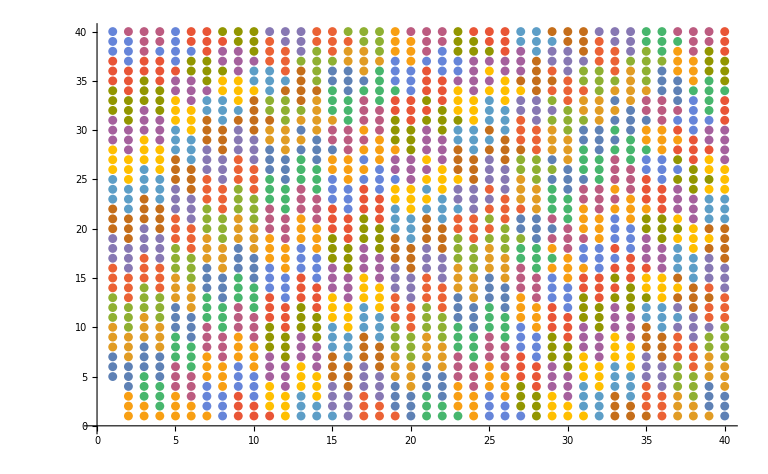

```mathematica
ListPlot[groups]
```

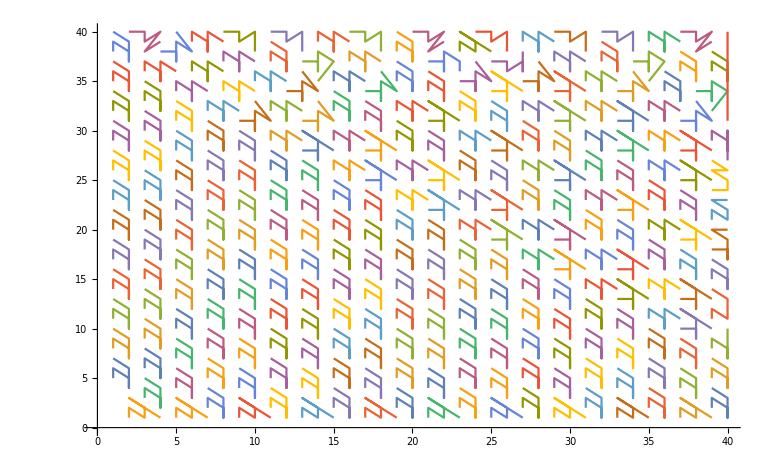

```mathematica
ListPlot[groups,Joined->True]
```

396 beams - MeerTRAP execution time VERY SMALL - Reports zero

```mathematica
data=Drop[Flatten[Table[{i,j},{i,1,20},{j,1,20}],1],4];
```

```mathematica
groups={};
```

```mathematica
Timing[Do[
group=Nearest[data,data[[1]],6];
data=Complement[data,group];
groups=Append[groups,group]
,{i,1,66}]]
```

{0.01563,Null}

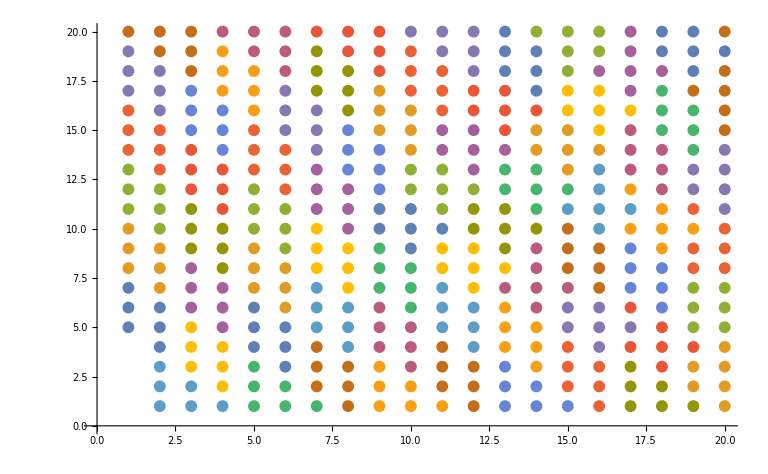

```mathematica
ListPlot[groups]
```

Realistic

```mathematica
distance[ra1_,dec1_,ra2_,dec2_]:=ArcCos[Sin[dec1]*Sin[dec2]+Cos[dec1]*Cos[dec2]*Cos[ra1-ra2]]
```

90^o

```mathematica
data1=Import[StringJoin[NotebookDirectory[],"134.0696_90.0_beam_pos.dat"],"Table"];
```

```mathematica
Length[data1];
data1=Drop[data1,-7];
Length[data1]
```

396

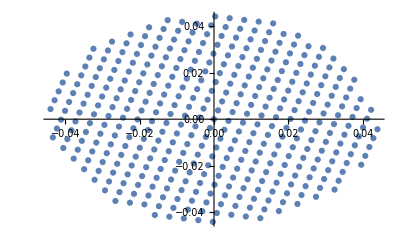

```mathematica
ListPlot[data1]
```

```mathematica
groups={};
```

```mathematica
data1=Sort[data1,#1[[1]]<#2[[1]]&];
```

```mathematica
Timing[Do[
distlist=Table[{data1[[i,1]],data1[[i,2]],distance[data1[[i,1]],data1[[i,2]],data1[[1,1]],data1[[1,2]]]},{i,2,Length[data1]}];
distlist=Sort[distlist,#1[[3]]<#2[[3]]&];

group=Insert[Table[{distlist[[i,1]],distlist[[i,2]]},{i,1,5}],data1[[1]],1];
data1=Complement[data1,group];
groups=Append[groups,group]
,{j,1,66}]]
```

{1.51563,Null}

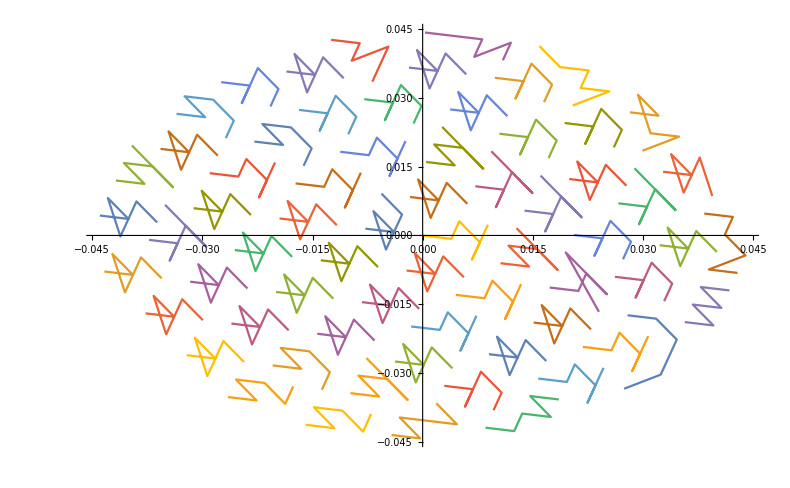

```mathematica
ListPlot[groups,Joined->True]
```

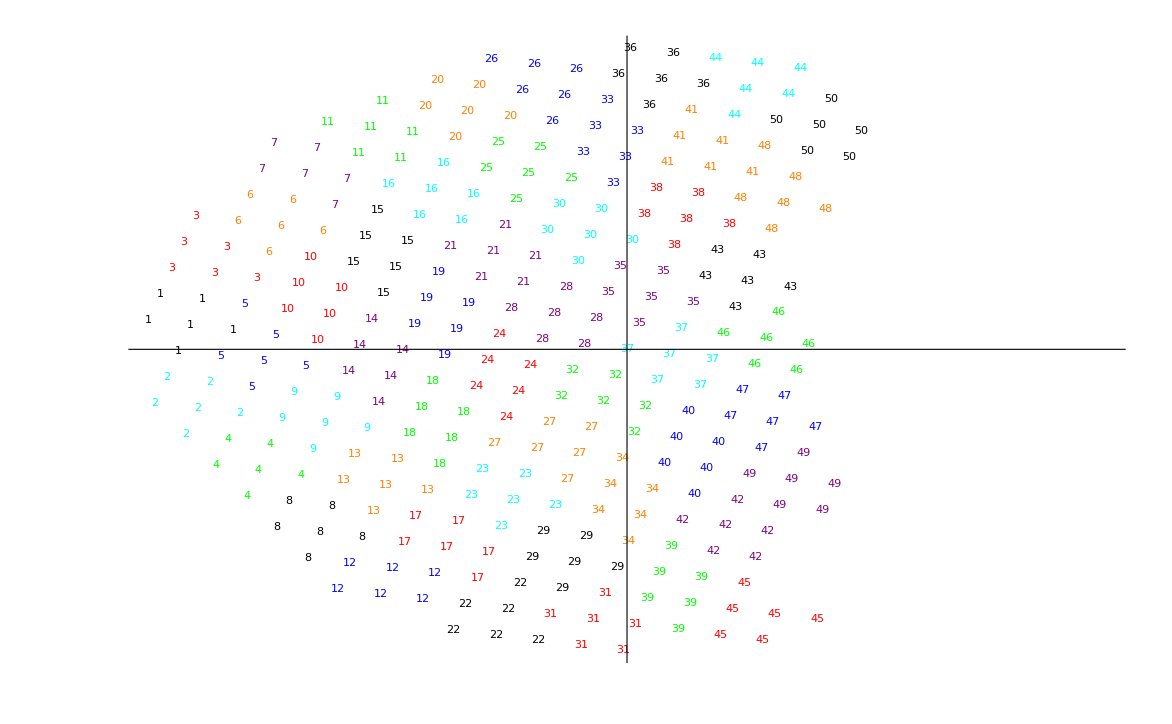

```mathematica
ListPlot[groups,PlotMarkers->marks,BaseStyle->{13,Bold},PlotStyle->{Black,Cyan,Red,Green,Blue,Orange,Purple,Black,Cyan,Red,Green,Blue,Orange,Purple,Black,Cyan,Red,Green,Blue,Orange,Purple,Black,Cyan,Red,Green,Blue,Orange,Purple,Black,Cyan,Red,Green,Blue,Orange,Purple,Black,Cyan,Red,Green,Blue,Orange,Purple,Black,Cyan,Red,Green,Blue,Orange,Purple,Black,Cyan,Red,Green,Blue,Orange,Purple,Black,Cyan,Red,Green,Blue,Orange,Purple,Black,Cyan,Red},Ticks->False]
```

```mathematica
data1=Import[StringJoin[NotebookDirectory[],"134.0696_90.0_beam_pos.dat"],"Table"];
```

```mathematica
data1=Drop[data1,-7];
```

```mathematica
groups={};
```

```mathematica
data1=Sort[data1,#1[[1]]<#2[[1]]&];
```

```mathematica
Timing[Do[
group=Nearest[data1,data1[[1]],6];
data1=Complement[data1,group];
groups=Append[groups,group]
,{i,1,66}]]
```

{0.0625,Null}

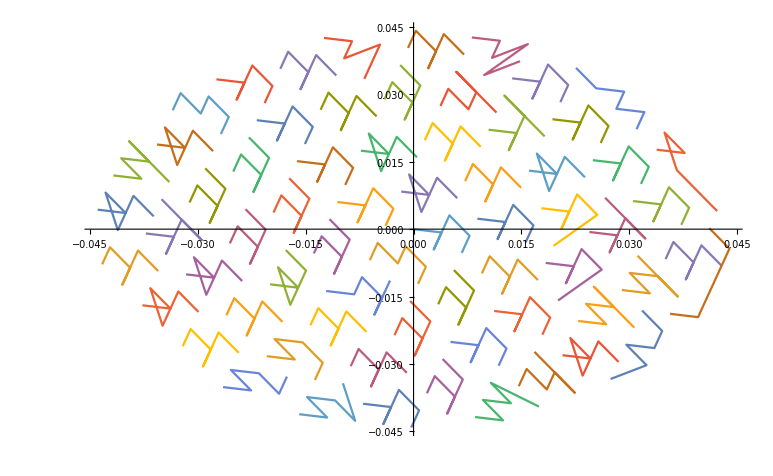

```mathematica
ListPlot[groups,Joined->True]
```

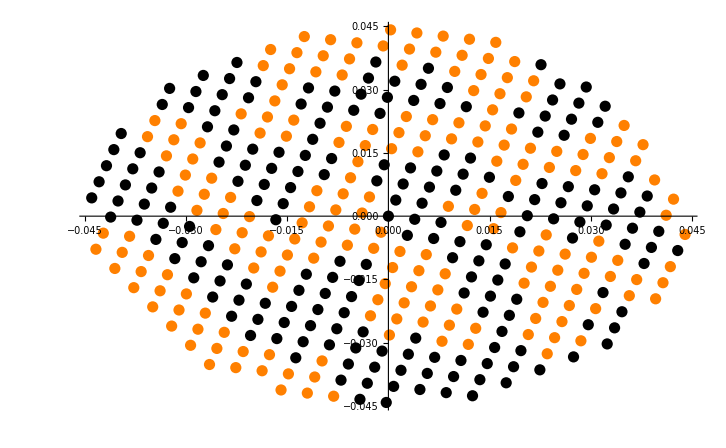

```mathematica
ListPlot[groups,PlotStyle->{Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange,Black,Orange}]
```

45^o

```mathematica
data2=Import[StringJoin[NotebookDirectory[],"134.0696_45.0_beam_pos.dat"],"Table"];
```

```mathematica
Length[data2]
```

407

```mathematica
data2=Drop[data2,-11];
```

```mathematica
Length[data2]
```

396

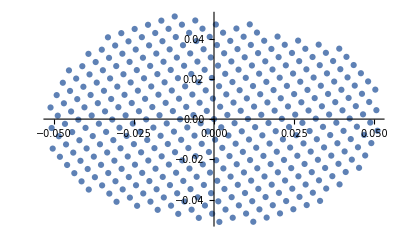

```mathematica
ListPlot[data2]
```

```mathematica
groups={};
```

```mathematica
data2=Sort[data2,#1[[1]]<#2[[1]]&];
```

```mathematica
Timing[Do[
group=Nearest[data2,data2[[1]],6];
data2=Complement[data2,group];
groups=Append[groups,group]
,{i,1,66}]]
```

{0.01563,Null}

```mathematica
ListPlot[groups,Joined->True]
```

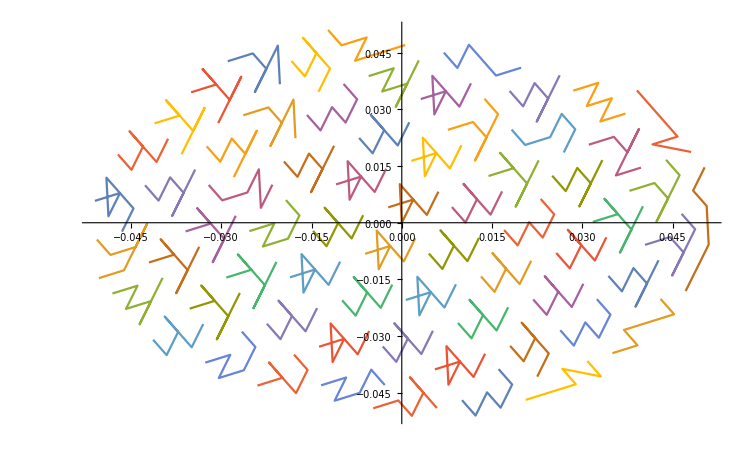

0^o

```mathematica
data3=Import[StringJoin[NotebookDirectory[],"134.0696_0.0_beam_pos.dat"],"Table"];
```

```mathematica
Length[data3]
```

407

```mathematica
data3=Sort[data3,#1[[1]]<#2[[1]]&];
```

```mathematica
data3=Drop[data3,-11];
```

```mathematica
Length[data3]
```

396

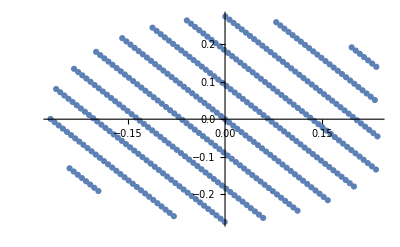

```mathematica
ListPlot[data3]
```

```mathematica
groups={};
```

```mathematica
Timing[Do[
distlist=Table[{data3[[i,1]],data3[[i,2]],distance[data3[[i,1]],data3[[i,2]],data3[[1,1]],data3[[1,2]]]},{i,2,Length[data3]}];
distlist=Sort[distlist,#1[[3]]<#2[[3]]&];

group=Insert[Table[{distlist[[i,1]],distlist[[i,2]]},{i,1,5}],data3[[1]],1];
data3=Complement[data3,group];
groups=Append[groups,group]
,{j,1,66}]]
```

{0.96875,Null}

```mathematica
Timing[Do[
group=Nearest[data3,data3[[1]],6];
data3=Complement[data3,group];
groups=Append[groups,group]
,{i,1,66}]]
```

{0.03125,Null}

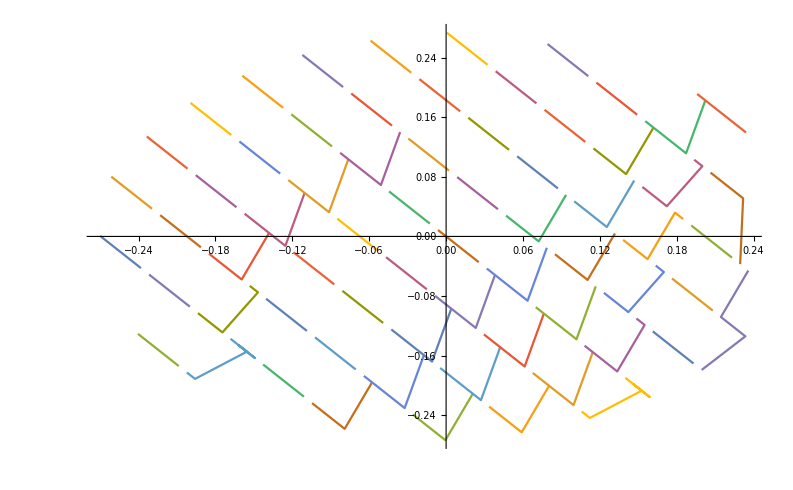

```mathematica
ListPlot[groups,Joined->True]
```

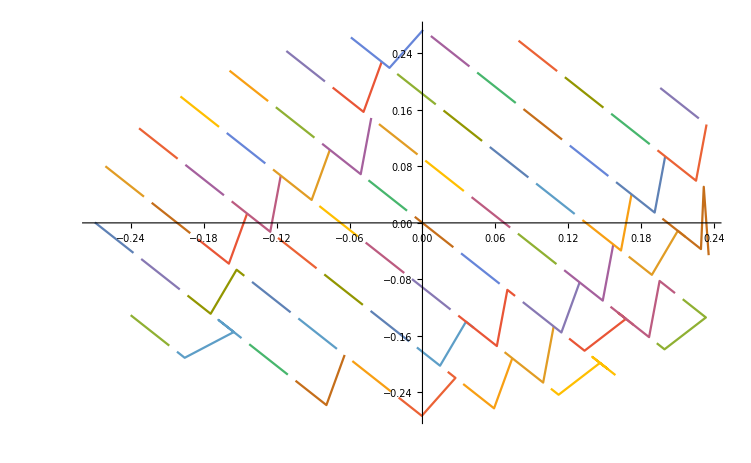

```mathematica
ListPlot[groups,Joined->True]
```

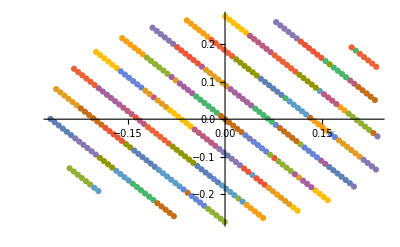

```mathematica
ListPlot[groups]
```

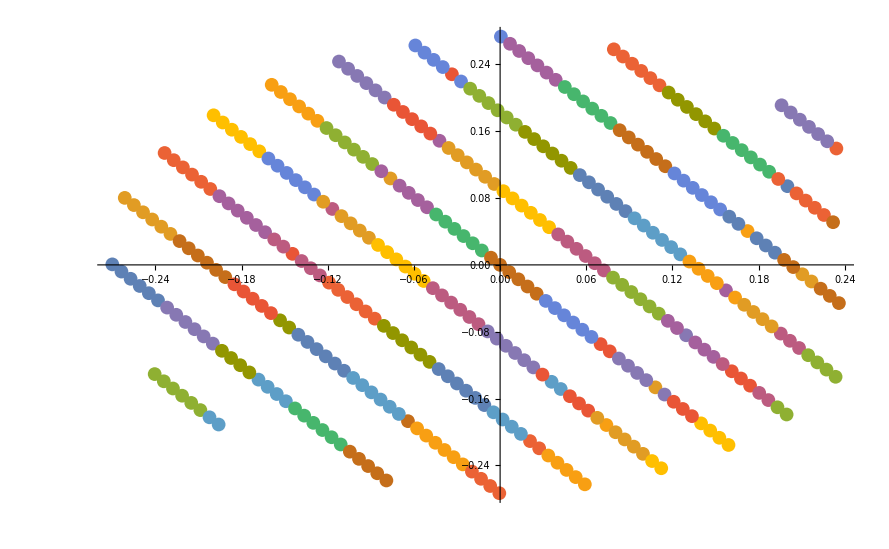

```mathematica
ListPlot[groups]
```